# Problem Set 1

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/PS2/code"];
```

## Question 1

```mathematica
1.5*0.03+(1-1.5)*0.05
```

0.02

```mathematica
1.5*0.07+(1-1.5)*0.05
```

0.08

```mathematica
4.5*0.03+(1-4.5)*0.05
```

-0.04

```mathematica
4.5*0.07+(1-4.5)*0.05
```

0.14

Consumption - savings

```mathematica
cS[δ_,ψ_,μ_]:=(ψ*δ+(1-ψ)*μ)/(1-(ψ*δ+(1-ψ)*μ))
```

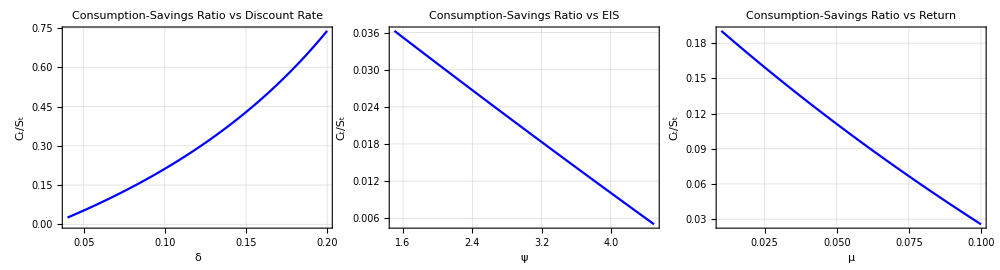

```mathematica
cSδ= Plot[{cS[δ,2.5,0.05]},{δ,0.04,0.2},
PlotStyle->{Blue},
PlotLabel->"Consumption-Savings Ratio vs Discount Rate",
FrameLabel->{"δ","C_t/S_t"},
Frame->True,
GridLines->Automatic];
cSψ= Plot[{cS[0.04,ψ,0.05]},{ψ,1.5,4.5},
PlotStyle->{Blue},
PlotLabel->"Consumption-Savings Ratio vs EIS",
FrameLabel->{"ψ","C_t/S_t"},
Frame->True,
GridLines->Automatic];
cSμ= Plot[{cS[0.07,2.5,μ]},{μ,0.01,0.10},
PlotStyle->{Blue},
PlotLabel->"Consumption-Savings Ratio vs Return",
FrameLabel->{"μ","C_t/S_t"},
Frame->True,
GridLines->Automatic];
consumptionSavings=GraphicsGrid[{{cSδ,cSψ,cSμ}},Spacings->-20,ImageSize->{1000,270}]
Export["images/consumption-savings.jpeg",consumptionSavings];
```